Grade 100. A+

# Math 154 SPRING 2013 Mario L Gutierrez Lesson 1

## Working in groups

I know you are going to work in groups. That’s OK, and there will be no penalty. But it is essential that when you work in a group you all understand your results, otherwise you won’t have learned and will be marooned later in the course. When you have worked in a group on a problem I want to see the names of the others with whom you have worked. That way I will only have to grade the problem once, and give detailed comments once.

## Reading

We use S as an abbreviation for Schaum’s and R as  an abbreviation for Ruskeepa. Read S ch 1,and 2.1-2.3 and R ch1,ch2. I will expect you to be familiar with the commands introduced in the reading.

We use execute,evaluate,enter and input, and call synonymously. We use result ,return and output synonymously. There is a Mathematica command Evaluate[], when we use the word evaluate we don’t mean use this command. 

It is amusing to note that Mathematica automatically italicizes her name.

 Edit>>Spellcheck is your friend. Use it!

Comment: execute all input cells as you encounter them. If you don’t do so you will fail to understand the lesson, and you may encounter wrong results later in the lesson. As you encounter new commands you should try out your own examples. You can only learn Mathematica by doing.

Convention: When I am mentioning a Mathematica command I will write it in bold-face. Thus:

When I give the command for the first time I will try to give its syntax. Thus (S1.9 ex 34)
Plot[expr,{var,lowerbound,upperbound}] is the syntax of the Plot command

```mathematica
Plot[Sin[30Cos[time]],{time,-5,10}]
```

Mathematica is totally picky about syntax. If you make a syntax mistake She will either tell you so in an orange warning message(in a probably incomprehensible way) or give wrong output. When inputting you should try to have some idea of what the form of the output should be. If you get a completely unexpected form you should be suspicious of whether you have input the right expression. Don’t just merrily continue on. Try to figure out what your error is, and if you can’t do so ask me a question.

## Mathematica 9 vs Mathematica 6

Almost every year a new version of Mathematica comes out and of course the Mathematica books don’t keep up. R. and S. are primarily discussing Mathematica 6 and we are working with Mathematica 9. As we come accross differences between Mathematica 6 and 9 I will discuss them. Read R 1.4.3. Mathematica 9 now provides command completions automatically as you type the name of the command and on the right side gives a link to the reference page for that command. As read R. first paragraph of p22 for command templates. Often you will forget the template and this is faster than looking up the command.

## Comments on Reading

```mathematica
Clear["Global`*"]
```

```mathematica
Clear["Global`*"]
```

When I say Query a command I mean that you should look it up in S., R. and the help Browser

Query the command N (decimal approximation) .Its syntax is N[number,precision]. Here the backrounding on the second argument indicates that it is optional. In text, phrases that occur in blue are hyperlinks. The hyperlinks  refer to pages in the help system or to url’s on the web. You should read them before proceeding.

#### S 1.2

You will find it handy to always have the basic math input palette open, and also the algebraic manipulation palette (Palettes>>other). There are keyboard shortcuts for many of the palette operations see the  document Keyboard Shortcuts on the course Blackboard site.Also read R 3.3.2 and R 3.3.2.

 Note that the semi-colon  ; after any command suppresses the output of that command. This is very handy if your output is going to be huge and you want to do something with the output, e.g. assign it to a variable but you don’t want to see the output. Otherwise you can find yourself in a situation where the output spans page after page.

```mathematica
a=N[π,500000];
```

```mathematica
b=N[π,500000]
```

```mathematica
Clear[a,b]
```

```mathematica
a=N[π,500000];
```

```mathematica
b=N[π,500000]
```

#### S 1.3

the symbols {,(,[ are left delimiters. Similarly },),} are right delimiters. Your delimiters must match up in pairs. Mathematica shows unmatched delimiters in purple. Thus

```mathematica
Plot[x^2,{x,1,2}
```

Shows that somewhere in this expression there is a missing ]. There is no use inputting an expression with unmatched delimiters. You will find Edit>>Check Balance very handy. A good idea is to type your delimiters in pairs and then backspace to fill them in. Otherwise matching delimiters can be a real struggle. Here is an example of what I mean by this: Suppose we with to input the expression Plot[x^2,{x,0,1}]. Here is the sequence of how I would suggest you type this:

Type
Plot
(then type[])
Plot[]
(then backspace and type  ,)
Plot[,]
(then type {})
Plot[,{}]
(then backspace and type  ,,)
Plot[,{,,}]
(now just fill in the slots)
Plot[x^2,{x,0,1}]

Reread and pay attention to the last paragraphs on S p3. I very strongly suggest that you stop and save every time you pause to think!, and certainly every time before you input a command. The little bit of extra-time you spend will be amply re-couped from the hours of work you can loose otherwise. I cannot tell you how many time I have lost hours of work by neglecting this suggestion. At least on my computer Mathematica can crash taking with it all your work since the last save.

#### S 1.4 Precision

There are three kinds of numerical quantities the so called exact or infinite precision quantities, examples are: integers,rational, complexes with rational coefficients, ⅇ,π , ⅈ and arithmetic combinations of these. Unlike the calculators that you have enountered Mathematica works with exact numbers with 100% precision. There is no rounding to a finite number of places. Then there are the MachinePrecision numbers these are numbers with approximately 16 significant digits. They are called machine precision because computers do arithmetic involving them using a part of the chip that they run on. Finally there are the higher precison, or software precision numbers examples are

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

#### S 1.6

1.6 The most common cells that you will use are input cells, text cells and DisplayFormula cells. It is a good idea to use Window>>Show Tool Bar. Text cells must be used for text. Reread the previous sentence 5 or 6 times. If you put text in an input cell I will penalize you. DisplayFormula cells are used for writing complicated mathematical expressions.

Example: Text Cell

Here is a text cell

Example: DisplayFormula cell.

∑_(i=1)^n i^2=1/4 n^2 (n+1)^2

Example: Input cell

```mathematica
N[ⅇ,22]
```

2.71828182845904523536

The last cell is an output cell.

You you can also write in-line mathematics in a text cell. Just type ctrl-9 start typing your formula and type ctrl-0 when you are done.  ,See the document on keyboard shortcuts. In-line mathematics is best used for short expressions. Example:

The Pythagorean theorem states that in a right-triangle √(adj^2+opp^2)=hyp. This is perhaps the oldest formula in geometry.

In this way once you get used to how you type with subscripts, superscripts,etc (See the blackboard document Mathematica Keyboard Short Cuts). Also read this tutorial: Entering Two dimensional Input you can use Mathematica as a mathematical word processor, and it superior to all such systems except LATEX ( see theWikipedia entry on LATEX. Disambiguate to mathematics).

1.7 To query a command is to look up the command in S, R and the document center. If you use the ? syntax the >> gets you to the page in the document center for the command. Always expand the More Information link. Whenever you encounter a command for the first time you should query it. Generally S will give lots of examples of the use of a command. The explanations in the document center can be obscure. They are written for mathematicians. The only way to learn is to  experiment with your own examples in a scratch notebook.

Comment: Mathematica places heavy demands on your computer. It can easily crash itself, or even your computer. Thus you must save your work frequently, perhaps every time you pause to think. Also Mathematica saves a lot of results you might not expect it to, so it can use a lot of memory. It is a good idea to quit the kernel every so often, Evaluation>>Quit Kernel. More radically, it is not a bad idea to occasionally restart your computer. You can always get back to where you were in a notebook with all input cells evaluated by using Evaluation>>Evaluate Notebook. It is also a good idea to have as few programs as possible running during a Mathematica session. In particular no movies  should be playing on your computer.

Read S 1.7, R1.4.2 It is a good idea to have at least two help windows open at any given time

2.1 One of the most common errors is to use e for ⅇ or i for ⅈ. Mathematica treats e and i as symbols with no predefined value. You can also type E or Pi.

#### S 1.6

Read S 1.6 a R3.1.2 first two paragraphs The most common cells that you will use are input cells, text cells and DisplayFormula cells. It is a good idea to use Window>>Show Tool Bar. Text cells must be used for text. Reread the previous sentence 5 or 6 times. If you put text in an input cell I will penalize you. DisplayFormula cells are used for writing complicated mathematical expressions.

Example: Text Cell

Here is a text cell

Example: DisplayFormula cell.

∑_(i=1)^n i^2=1/4 n^2 (n+1)^2

Example: Input cell

```mathematica
N[ⅇ,22]
```

2.71828182845904523536

The last cell is an output cell.

You you can also write in-line mathematics in a text cell. Just type ctrl-9 start typing your formula and type ctrl-0 when you are done.  ,See the document on keyboard shortcuts. In-line mathematics is best used for short expressions. Example:

The Pythagorean theorem states that in a right-triangle √(adj^2+opp^2)=hyp. This is perhaps the oldest formula in geometry.

In this way once you get used to how you type with subscripts, superscripts,etc (See the blackboard document Mathematica Keyboard Short Cuts) you can use Mathematica as a mathematical word processor, and it superior to all such systems except LATEX ( see theWikipedia entry on LATEX. Disambiguate to mathematics).

#### S 1.7

Read S 1.7 . Also read R 1.4.2. To query a command is to look up the command in S, R and the document center. If you use the ? syntax the >> gets you to the page in the document center for the command. Always expand the More Information link. Whenever you encounter a command for the first time you should query it. Generally S will give lots of examples of the use of a command. The explanations in the document center can be obscure. They are written for mathematicians. The only way to learn is to  experiment with your own examples in a scratch notebook.

Comment: Mathematica places heavy demands on your computer. It can easily crash itself, or even your computer. Thus you must save your work frequently, perhaps every time you pause to think. Also Mathematica saves a lot of results you might not expect it to, so it can use a lot of memory. It is a good idea to quit the kernel every so often, Evaluation>>Quit Kernel. More radically, it is not a bad idea to occasionally restart your computer. You can always get back to where you were in a notebook with all input cells evaluated by using Evaluation>>Evaluate Notebook. It is also a good idea to have as few programs as possible running during a Mathematica session. In particular no movies  should be playing on your computer.

### S Ch 2

Read it all, skipping 2.8 for the time being. I will comment on some of the sections. You need to read each section and to try read and understand each of the examples. Also a good student would work through each of the solved problems without looking at the answers.

#### S 2.1

One of the most common errors is to use e for ⅇ or i for ⅈ. Mathematica treats e and i as symbols with no predefined value. You can also type E or Pi or I.

#### S 2.2

Read S 2.2 to get a vocabulary of functions. As you meet a function query it and work a couple of examples. If you really want to learn Mathematica you should work through the Solved Problems as you read each section of Schuams.

Query RandomInteger,RandomReal,and RandomComplex.

#### Forms

Read R. 3.3.1. Query: TraditionalForm,InputForm, and FullForm. Traditional Form is useful when you want an expression to be displayed as it would be in a math textbook. InputForm is useful when you want an expression written with only the symbols on a standard keyboard, so that,e.g., you can cut and paste their result into an e-mail. If you are familiar with Wolfram Alpha , wolframalpha.com, you can paste expressions in InputForm into Alpha and get a result. This is handy if you want a friend to be able to evaluate a line of Mathematica code: Put the code into input form, e-mail it to them, and then have them paste the line into Alpha.

```mathematica
1+x+x^2//TraditionalForm
```

x^2+x+1

```mathematica
D[f[x],{x,2}]//TraditionalForm
```

f''(x)

```mathematica
Integrate[f[x],{x,3,7}]//TraditionalForm
```

∫_3^7 f(x)ⅆx

```mathematica
∫_3^7 f(x)ⅆx//InputForm
```

Integrate[f[x], {x, 3, 7}]

```mathematica
x^2+x/y^2+∫_1^2 f[x]ⅆx//InputForm
```

```mathematica
x^2+x/y^2+∫_1^2 f[x]ⅆx//TraditionalForm
```

∫_1^2 f(x)ⅆx+x^2+x/y^2

```mathematica
D[f[z]^2,z]
```

2 f[z] f'[z]

```mathematica
D[f[z]^2,z]//TraditionalForm
```

2 f(z) f'(z)

```mathematica
x^2+x/y+x+1//FullForm
```

Plus[1,x,Power[x,2],Times[x,Power[y,-1]]]

FullForm is Mathematica’s internal representation of an expression and it will be useful to know what the FullForms of expressions are. You can use FullForms for input.

```mathematica
x+y//FullForm
```

Plus[x,y]

```mathematica
Plus[2,3]
```

```mathematica
x+y+z//FullForm
```

Plus[x,y,z]

```mathematica
x y//FullForm
```

Times[x,y]

```mathematica
x^y//FullForm
```

Power[x,y]

```mathematica
Power[x,y]
```

x^y

```mathematica
x/y//FullForm
```

Times[x,Power[y,-1]]

```mathematica
FullForm[12/10]
```

Rational[6,5]

```mathematica
FullForm[3+5ⅈ]
```

Complex[3,5]

## S 2.5 Three kinds of equality.

Read S 2.5. For the time being skip examples 38 and 49.

#### =,=:

The random functions give perhaps the best example of the difference between = and := . As we have seen a=b  sets a to be the value of b at the time that the command is entered. The symbol a then retains this value until it is cleared. We also call this assigning the value of b to a, or setting a to be b. a=b is called an immediate assignment. Whereas a:=b means that each time a is input it gets the value of b at the time we input a. a:=b  is called delayed assignement.

```mathematica
b=7
```

7

```mathematica
a=b
```

7

```mathematica
a
```

7

```mathematica
b=3
```

3

```mathematica
a
```

7

```mathematica
a:=b
```

Notice that delayed assignment gives no output. (It is actually giving the output Null but let's leave the explication of Null until later).

```mathematica
b=7
```

7

```mathematica
a
```

a

```mathematica
b=21
```

21

```mathematica
a
```

21

```mathematica
Clear[a,b]
```

The various random functions give a good example of the difference between immediate assignment and delayed assignment.

##### Random Number generators

2.2 Random is obsolete as of Mathematica 7. Use RandomInteger, RandomReal or RandomComplex. Query these commands.  In a scratch experiment with examples.

```mathematica
cr=RandomReal[{-5,10}]
```

Mathematica calls the RandomReal function and then assigns its value to cr. The symbol cr then has this value until it is cleared

```mathematica
cr
```

```mathematica
cr
```

```mathematica
cr
```

```mathematica
Clear[cr]
```

As opposed to 
Delayed assignment:

```mathematica
dr:=RandomReal[{-5,10}]
```

This delayed assignment is telling Mathematica that each time dr is input we should evaluate the RandomReal function and assign its value to dr.

```mathematica
dr
```

```mathematica
dr
```

```mathematica
dr
```

```mathematica
Clear[dr]
```

#### S 2.6 ==

Query ==  Query Equal

```mathematica
FullForm[a==b]
```

Equal[a,b]

The symbol == is typed as two equal signs one immediately after the other. It is used to test equality of expressions , that is it is used for equations. Inputting expr_1==expr_2 gives True when the two expressions are equal, False when the two expressions are unequal, and returns unevaluated, that is the output is the same as the input, when the two expressions contain unassigned symbols, and have different Mathematica FullForm

```mathematica
2==2
```

```mathematica
3==2
```

```mathematica
Clear[x]
```

```mathematica
x+1==x
```

```mathematica
(1+x)^2==x^2+2x+1
```

Here our input is returning unevaluated because x is unassigned.

```mathematica
FullForm[(1+x)^2]
```

```mathematica
FullForm[x^2+2x +1]
```

```mathematica
x^2+2x+1==1+x^2+2x
```

True

```mathematica
FullForm[x^2+2x+1]
```

```mathematica
FullForm[1+x^2+2x]
```

At first the result of inputting expr_1==expr_2 is confusing. All I can say is that with practice the meaning of == will become clearer. A classic Mathematica error is typing = when you meant ==. If you commit this error you get an unintended assignment, which you will need to Clear, typically with the =. syntax before you can proceed.

Read S 7.1-7.3. Be sure to query the commands as you encounter them.

Query the Timing command. Be sure you understand the syntax Timing[Command;], be prepared to have a cup of coffee, or see a crash while the following command executes, on my computer it takes 10 minutes. My chip is not particularly fast

```mathematica
Timing[N[π,200000000];]
```

Currently π is know to about 4000000000 places. One of the ways that new supercomputers are tested is to ask them to compute a large number of digits of π, and compare to computations on well tested supercomputers. Sometimes the programmers and designers have to go back to their whatchamacallits (once upon a time we called them drawing boards) and rework. Once in the late 90’s Intel’s chip designers made a mistake that caused intermittent arithmetic errors. They had a hard time finding where the error lay and there was a massive recall of computers.

### Replacement

Query ReplaceAll. S p 41 ex 41,42,43. Read and understand the problem 2.41-2.45. Read R. 13.1.2. Read the tutorial ApplyingTransformationRules

### Complex Numbers

Mathematica is designed for working mathematicians and as such makes no assumptions about whether a number is real or complex. Exponents can be real or  complex, as can be the arguments of the standard transcendental functions.

```mathematica
(3+4I)/(11+6I)
```

57/157+(26 ⅈ)/157

```mathematica
1.2^I
```

0.983425+0.181313 ⅈ

```mathematica
(1+3.1I)^(4+5I)
```

-0.0116559-0.207682 ⅈ

```mathematica
Cos[5.2 I]
```

90.6389+0. ⅈ

```mathematica
ArcTan[4.5 I]
```

1.5708+0.225993 ⅈ

Query Re,Im and ComplexExpand.

Odd roots of negative numbers are complex:

```mathematica
a=(-1)^(1/3)
```

(-1)^(1/3)

```mathematica
N[a]
```

0.5+0.866025 ⅈ

```mathematica
Re[a]
```

1/2

```mathematica
Im[a]
```

(√3)/2

```mathematica
ComplexExpand[a]
```

1/2+(ⅈ √3)/2

```mathematica
Clear[a]
```

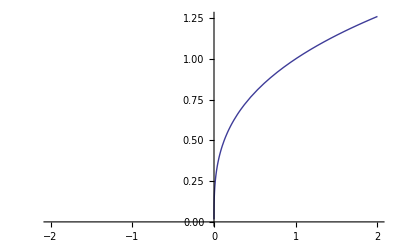

```mathematica
Plot[x^(1/3),{x,-2,2}]
```

We only see a plot over the right hand side because for x≤0 x^(1/3) is non-real

Furthermore many of the standard identites for exponentiation don’t work for negative numbers e.g ((-1)^a)^b is not in general (-1)^(a b).

```mathematica
a=((-1)^3)^(1/5)
```

(-1)^(1/5)

```mathematica
b=((-1)^(1/5))^3
```

(-1)^(3/5)

```mathematica
ComplexExpand[a]
```

1/4+(√5)/4+ⅈ √(5/8-(√5)/8)

```mathematica
ComplexExpand[b]
```

1/4-(√5)/4+ⅈ √(5/8+(√5)/8)

```mathematica
Clear[a,b]
```

New In Mathematica 9 are the commands Surd and CubeRoot

```mathematica
(-3.1)^(1/3)
```

0.72905+1.26275 ⅈ

```mathematica
%^3
```

-3.1+8.88178×10^-16 ⅈ

Observe there is a slight round off error because we are working with machine precision

```mathematica
Surd[-3.1,3]
```

-1.4581

```mathematica
%^3
```

-3.1

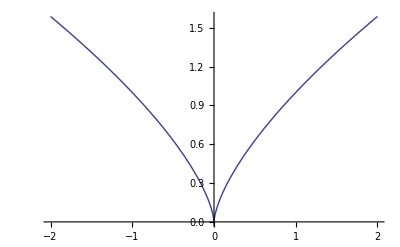

```mathematica
Plot[Surd[x,3]^2,{x,-2,2}]
```

### S 2.9 Elementary Graphing

Read S 2.9 be particularly sure to do all the problems.

## The Drawing Tools:

Mathematica also has a very sophisticated set of drawing tools. Read R 5.1.3 and Interactive Graphics Palette. One of the most useful tools is   Get Coordinates Tool. It allows us to get the coordinates of a point in a two dimensional graphic. This is also what allows us to mark points in a graphic and then get a list of their coodinates,in order of marking, copied into an input cell. The best I can do is try to explain an example. Let’s get of the approximate coordinates of the points of intersection in the following graphic starting from the upper left hand side and proceeding in clock wise order

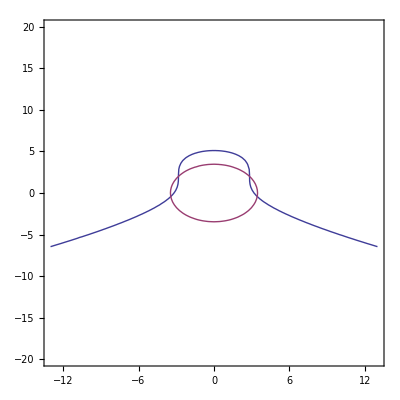

```mathematica
a=ContourPlot[{x^2/8+(y-2)^3/30==1,x^2+y^2==12},{x,-13,13},{y,-20,20}]
```

From the graphics menu click on drawing tools. Since we are going to mark several points  click on the get coordinates tool (the crossed dots). Now go to the graphic move the crossed dots to the first crossing click and hit ⌘-c on a mac or Ctrl-c in windows. Proceed counter-clockwise until you have done this with all 4 crossings. You have a list of points on your clipboard. Just hit ⌘-v or Ctrl-v to copy this list into an input cell.

```mathematica
{{-2.665,2.029},{2.833,1.906},{3.311,-0.3003},{-3.462,-0.6681}}
```

## Problems Lesson 1

Query the commands: 
Denominator
Numerator
Expand
Factor
FactorList
FactorInteger
Together
TrigExpand
TrigReduce.

Also query Simpify and FullSimplify. For Simplify and FullSimplify pay particular attention to R 32 and R.13.2.1and S 7.4.

Query OddQ,EvenQ,IntegerQ,ExactNumberQ,NumberQ, and NumericQ. You may think of the ending Q as shorthand for question.

Ususally the problems and exercises for a lesson will come interspersed among the text of the lesson. Because there was so much reading in this lesson I have ended it with exercises and problems

The natural logarithm shows up all through mathematics. Logs base 2 are central to computer science. Logs base 10 are an accident of living on a planet where the dominant species happens to have 10 digits, and are not of much intrinsic interest.

## Answers Problems Lesson 1

Ususally the problems and exercises for a lesson will come interspersed among the text of the lesson. Because there was so much reading in this lesson I have ended it with exercises and problems

Query the commands Log,Ceiling and Floor

The natural logarithm shows up all through mathematics. Logs base 2 are central to computer science. Logs base 10 are an accident of living on a planet where the dominant species happens to have 10 digits, and are not of much intrinsic interest.

Problem 1: (10 points) Use Mathematica to show that tan(3π/11)+4sin(2π/11)=√11. Show how long Mathematica takes to do the computation Some hints since you are just beginning to use Mathematica: the expression on the left is input

Tan[3π/11]+4 Sin[2π/11]

That is Mathematica built in function names begin with uppercase letters and we input f(x) with the argument surrounded by square-brackets []. Secondly you may need to use Simplify or FullSimplify.

```mathematica
Timing[FullSimplify[Tan[3π/11]+4 Sin[2π/11]]]
```

{0.00016,Cot[(5 π)/22]+4 Sin[(2 π)/11]}

```mathematica
Timing[Simplify[Tan[3π/11]+4 Sin[2π/11]]]
```

{0.00015,Cot[(5 π)/22]+4 Sin[(2 π)/11]}

10 points.

Problem 2: (10 points) Between what two powers of 2 is 10^30000000+3^24533845.

```mathematica
Floor[Log[2,10^30000000+3^24533845]]
```

99657842

```mathematica
Ceiling[Log[2,10^30000000+3^24533845]]
```

99657843

The number lies between the 99657842^nd and the 99657843^rd powers of 2 .

Problem 3: (15 points)

 	a: How long does it take your computer to calculate ⅇ rounded to 10000000 digits after the decimal point?

```mathematica
Timing[N[ⅇ,10000001];]
```

{7.09925,Null}

b: Run this computation again

```mathematica
Timing[N[ⅇ,10000001];]
```

{7.11553,Null}

c : Something strange is happening. Describe this event.

I do not see anything extraordinary going on. Am I missing anyhing??

15 points. See answers. This is one of those difference between Mathematica 9 and Mathematica 8!

Problem 3: (10 points) a: A Fermat prime is a prime number of the from 2^(2^n)+1. Find the first n such that 2^(2^n)+1 is not prime. b: Is 2^(2^16)+1 prime? How long on your computer does Mathematica take to figure out the answer? State your results in a sentence.

a:

```mathematica
PrimeQ[2^(2^5)+1]
```

False

b:

```mathematica
Timing[PrimeQ[2^(2^16)+1]]
```

{239.56308,False}

The given number "2^(2^16)" is not a prime. It took Mathematica approximately 240 seconds (roughly four minutes) on my computer to determine whether or not the input was a prime.

10 points. In part a how did you know that you could get up to 5?

Problem 4: (15 points) a: Factor x^m-1 for m=36,60,72. Make a conjecture about the coefficients of the factors of x^n-1 for n a natural number

```mathematica
m={26,60,72};
```

```mathematica
Factor[x^m-1]
```

{(-1+x) (1+x) (1-x+x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9+x^10-x^11+x^12) (1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10+x^11+x^12),(-1+x) (1+x) (1+x^2) (1-x+x^2) (1+x+x^2) (1-x^2+x^4) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4) (1-x^2+x^4-x^6+x^8) (1-x+x^3-x^4+x^5-x^7+x^8) (1+x-x^3-x^4-x^5+x^7+x^8) (1+x^2-x^6-x^8-x^10+x^14+x^16),(-1+x) (1+x) (1+x^2) (1-x+x^2) (1+x+x^2) (1+x^4) (1-x^2+x^4) (1-x^3+x^6) (1+x^3+x^6) (1-x^4+x^8) (1-x^6+x^12) (1-x^12+x^24)}

It seems like all the coefficients in the output are either 0,-1, or 1. Is that a correct conjecture ??

b: 105 is the first product of 3 odd primes. Factor x^105-1 is the result you get consistent with the conjecture you made in a?

```mathematica
Factor[x^105-1]
```

(-1+x) (1+x+x^2) (1+x+x^2+x^3+x^4) (1+x+x^2+x^3+x^4+x^5+x^6) (1-x+x^3-x^4+x^5-x^7+x^8) (1-x+x^3-x^4+x^6-x^8+x^9-x^11+x^12) (1-x+x^5-x^6+x^7-x^8+x^10-x^11+x^12-x^13+x^14-x^16+x^17-x^18+x^19-x^23+x^24) (1+x+x^2-x^5-x^6-2 x^7-x^8-x^9+x^12+x^13+x^14+x^15+x^16+x^17-x^20-x^22-x^24-x^26-x^28+x^31+x^32+x^33+x^34+x^35+x^36-x^39-x^40-2 x^41-x^42-x^43+x^46+x^47+x^48)

The conjecture (assuming it was correct!) does not seem to hold this time, as there is a -2 coefficient in the x^41 term.

15 points. Sometimes one makes a conjecture and it turns out to be false! Particularly many mathematical phenomena only show up beyond the point of pratical computation

Read S p60  and  61. Query the command  Length. Query the commands Divisors and FactorList.  When we evaluate FactorList on a polynomial with rational coefficients our first one or two factors are  polynomials of degree 0, that is a constant polynomial.

```mathematica
FactorList[3x-3/5]
```

{{3,1},{5,-1},{-1+5 x,1}}

The numbers 4!,5!,6! have lots of divisors.

Problem 5: (15 points)

Compare the number of non-constant factors of  x^m-1 with the numbers of divisors  of m, for m=4!,m=5! and m=6!. Make a conjecture about the comparison for m any natural number n.

```mathematica
FactorList[x^(4!)-1]
```

{{1,1},{-1+x,1},{1+x,1},{1+x^2,1},{1-x+x^2,1},{1+x+x^2,1},{1+x^4,1},{1-x^2+x^4,1},{1-x^4+x^8,1}}

```mathematica
Length[%]
```

9

```mathematica
Divisors[4!]
```

{1,2,3,4,6,8,12,24}

```mathematica
Length[%]
```

8

```mathematica
FactorList[x^(5!)-1]
```

{{1,1},{-1+x,1},{1+x,1},{1+x^2,1},{1-x+x^2,1},{1+x+x^2,1},{1+x^4,1},{1-x^2+x^4,1},{1-x+x^2-x^3+x^4,1},{1+x+x^2+x^3+x^4,1},{1-x^4+x^8,1},{1-x^2+x^4-x^6+x^8,1},{1-x+x^3-x^4+x^5-x^7+x^8,1},{1+x-x^3-x^4-x^5+x^7+x^8,1},{1-x^4+x^8-x^12+x^16,1},{1+x^2-x^6-x^8-x^10+x^14+x^16,1},{1+x^4-x^12-x^16-x^20+x^28+x^32,1}}

```mathematica
Length[%]
```

17

```mathematica
Divisors[5!]
```

{1,2,3,4,5,6,8,10,12,15,20,24,30,40,60,120}

```mathematica
Length[%]
```

16

```mathematica
FactorList[x^(6!)-1]
```

{{1,1},{-1+x,1},{1+x,1},{1+x^2,1},{1-x+x^2,1},{1+x+x^2,1},{1+x^4,1},{1-x^2+x^4,1},{1-x+x^2-x^3+x^4,1},{1+x+x^2+x^3+x^4,1},{1-x^3+x^6,1},{1+x^3+x^6,1},{1+x^8,1},{1-x^4+x^8,1},{1-x^2+x^4-x^6+x^8,1},{1-x+x^3-x^4+x^5-x^7+x^8,1},{1+x-x^3-x^4-x^5+x^7+x^8,1},{1-x^6+x^12,1},{1-x^8+x^16,1},{1-x^4+x^8-x^12+x^16,1},{1+x^2-x^6-x^8-x^10+x^14+x^16,1},{1-x^12+x^24,1},{1-x^3+x^9-x^12+x^15-x^21+x^24,1},{1+x^3-x^9-x^12-x^15+x^21+x^24,1},{1-x^8+x^16-x^24+x^32,1},{1+x^4-x^12-x^16-x^20+x^28+x^32,1},{1-x^24+x^48,1},{1+x^6-x^18-x^24-x^30+x^42+x^48,1},{1+x^8-x^24-x^32-x^40+x^56+x^64,1},{1+x^12-x^36-x^48-x^60+x^84+x^96,1},{1+x^24-x^72-x^96-x^120+x^168+x^192,1}}

```mathematica
Length[%]
```

31

```mathematica
Divisors[6!]
```

{1,2,3,4,5,6,8,9,10,12,15,16,18,20,24,30,36,40,45,48,60,72,80,90,120,144,180,240,360,720}

```mathematica
Length[%]
```

30

It seems like the number of divisors of any given natural number ‘n’ ( better mathematical writing is to italicize n)is the same as the number of non-constant factors found in the expression x^m-1  x^(n-1)The length of x^m-1 always have one more element than the the list of the number of divisors but this extra element is a constant factor (no variable present or x^0) ].

15 points

Query the command Mod. Observe that the number m ends in at least n zeros if 
Mod[m,10^n]=0.

Problem 6: (10 points).Show that 98^98×75^75ends in exactly 98 zeroes. Don't compute the product and then count the trailing zeros.

```mathematica
Mod[98^98*75^75,10^98]
```

0

```mathematica
Mod[98^98*75^75,10^99]
```

500000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

We can see that the remainder is zero when we divide by 10^98but that is not the case when we try that operation with 10^99.

10 points

Problem 7:(10 points). Show that 1+ the product of 4 consecutive integers is a perfect square. Hint: Factor

```mathematica
Factor[1+x (x+1)(x+2)(x+3)]
```

(1+3 x+x^2)^2

10 points